```mathematica
串联耦合摆的轨迹计算
```

```mathematica
10秒
```

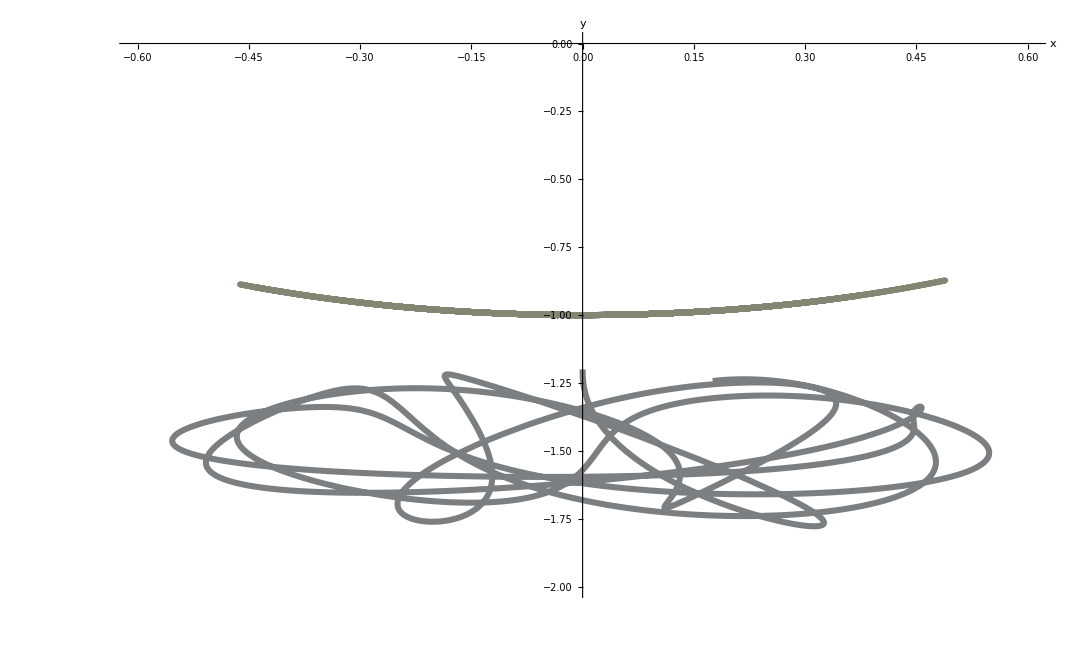

```mathematica
g=9.8;k=3;m1=0.1;m2=0.1;
L1=1;L2=0.2;tm=10;
initial1={0,1.4/L1};
initial2={0,0.0,-(L1+L2),0};
temp=2L1 (y2[t] Cos[θ[t]]-x2[t] Sin[θ[t]]);
L=√(x2[t]^2+y2[t]^2+L1^2+temp);
equs=
{θ''[t]==
(y2[t] Sin[θ[t]]+x2[t] Cos[θ[t]]) (1-L2/L) k/(m1 L1)
-g/L1 Sin[θ[t]],
x2''[t]==-(x2[t]-L1*Sin[θ[t]]) (1-L2/L) k/m2,
y2''[t]==-(y2[t]+L1 Cos[θ[t]]) (1-L2/L) k/m2-g,
θ[0]==initial1[[1]],θ'[0]==initial1[[2]],
x2[0]==initial2[[1]],x2'[0]==initial2[[2]],
y2[0]==initial2[[3]],y2'[0]==initial2[[4]]};
s=NDSolve[equs,{θ,x2,y2},{t,0,tm}];
{θ,x2,y2}={θ,x2,y2}/.s[[1]];
ParametricPlot[{{L1*Sin[θ[t]],-L1*Cos[θ[t]]},
{x2[t],y2[t]}},{t,0,tm},
PlotRange->{{-0.6,0.6},{-2,0}},
AxesLabel->{"x","y"},AspectRatio->0.6,
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003],ColorFunction->Function[{x,y,t},Hue[t]]]
Clear[g,equs,s,θ,x2,y2,initial1,initial2]
```

```mathematica
100秒
```

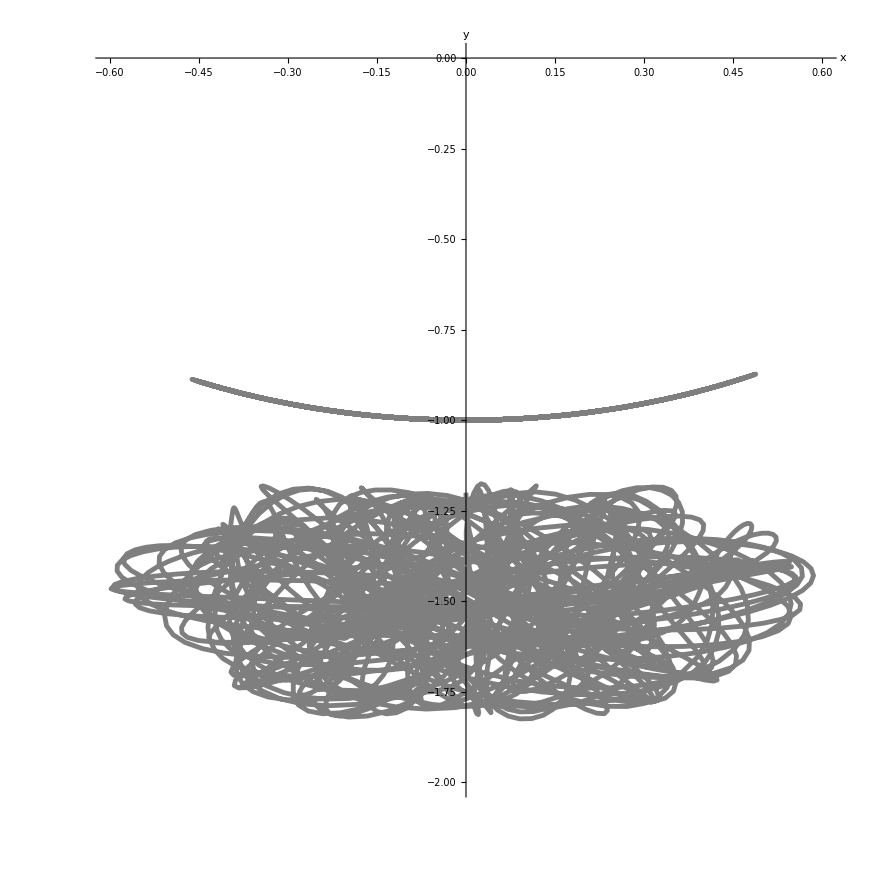

```mathematica
g=9.8;k=3;m1=0.1;m2=0.1;
L1=1;L2=0.2;tm=100;
initial1={0,1.4/L1};
initial2={0,0.0,-(L1+L2),0};
temp=2L1 (y2[t] Cos[θ[t]]-x2[t] Sin[θ[t]]);
L=√(x2[t]^2+y2[t]^2+L1^2+temp);
equs=
{θ''[t]==
(y2[t] Sin[θ[t]]+x2[t] Cos[θ[t]]) (1-L2/L) k/(m1 L1)
-g/L1 Sin[θ[t]],
x2''[t]==-(x2[t]-L1*Sin[θ[t]]) (1-L2/L) k/m2,
y2''[t]==-(y2[t]+L1 Cos[θ[t]]) (1-L2/L) k/m2-g,
θ[0]==initial1[[1]],θ'[0]==initial1[[2]],
x2[0]==initial2[[1]],x2'[0]==initial2[[2]],
y2[0]==initial2[[3]],y2'[0]==initial2[[4]]};
s=NDSolve[equs,{θ,x2,y2},{t,0,tm}];
{θ,x2,y2}={θ,x2,y2}/.s[[1]];
ParametricPlot[{{L1*Sin[θ[t]],-L1*Cos[θ[t]]},
{x2[t],y2[t]}},{t,0,tm},
PlotRange->{{-0.6,0.6},{-2,0}},
AxesLabel->{"x","y"},AspectRatio->1,
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003],ColorFunction->Function[{x,y,t},Hue[t]]]
Clear[g,equs,s,θ,x2,y2,initial1,initial2]
```